```mathematica
Clear["Global`*"];
```

# 数值积分与数值微分

申奥 2017012518 计科70

## 实验目的

本实验的目的是实现几种数值计算积分的方法，同时实现对数值积分步长 h 进行先验估计，在有绝对误差限制的条件下给出近似积分的值。

## 算法原理与代码实现

在已知步长的情况下，复合辛普森公式根据课本可以直接利用求和方式实现：

```mathematica
simpsonIntegrate[f_,a_,b_,n_]:=Block[{x,h=Abs[b-a]/n},
x/:Subscript[x,s_]:=a+s×h;
h/6(f[a]+f[b]+4(∑_(k=0)^(n-1) f[Subscript[x, k+1/2]])+2(∑_(k=1)^(n-1) f[Subscript[x, k]]))
]
```

以下我们考虑对辛普森公式进行步长的先验估计。已经知道，辛普森公式的余项由 -1/2880 h^4(b-a) f^(4)(n) 给出。我们需要根据函数高阶导数的图象，估计其余项的取值范围，并以此估计步长 h 的取值范围。

```mathematica
simpsonR[f_,a_,b_,h_]:=-1/2880 h^4(b-a)Derivative[4][f][#(*η*)]&
```

上式本身含有一个不定值η。

对于函数 1/x，注意其四阶导数单调递减，因此余项的上限取为 η=1 时，即
I(f)-S_n=-1/2880 h^4(b-a) f^(4)(n)≤-1/2880h^4(b-a)f^(4)(1)。为使其满足绝对误差要求，我们有

```mathematica
Reduce[Abs[simpsonR[1/#&,1,2,1/n][1]]<10^-8/2,Reals]//N
```

Abs[n]<-35.9304||Abs[n]>35.9304

取步长 h=1/36 ，计算得到

```mathematica
simpsonIntegrate[1/#&,1.`10,2.`10,36]
```

0.693147182

精确值 ln(2) 应为

```mathematica
N[Log[2],10]
```

0.6931471806

其误差确实符合相应的误差要求。

同样，对于函数 1/(1+x^2)，其四阶导数的图像如下

-(96 x^2)/((1+x^2)^4)+16/((1+x^2)^3)-2 ((24 x^2)/((1+x^2)^4)-4/((1+x^2)^3))-2 x ((48 x)/((1+x^2)^4)-4 x ((48 x^2)/((1+x^2)^5)-6/((1+x^2)^4)))

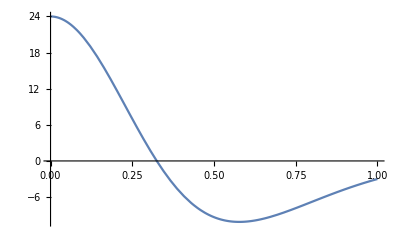

```mathematica
Derivative[4][1/(1+#^2)&][x]
Plot[Derivative[4][1/(1+#^2)&][x],{x,0,1}]
```

可以看到在 η=0 时残差有最大值，为满足误差要求，需要

```mathematica
Reduce[Abs[simpsonR[1/(1+#^2)&,0,1,1/n][0]]<10^-8/2,Reals]//N
```

Abs[n]<-35.9304||Abs[n]>35.9304

仍取步长 h=1/36 计算得

```mathematica
4simpsonIntegrate[1/(1+#^2)&,0,1.`10,36]
```

3.14159265

精确值应为

```mathematica
N[Pi,10]
```

3.141592654

两者之差确实符合精度要求。

对于 Romberg 外推方法，每次外推所得的值可以采用公式得到。对于第 k 次外推序列第 n 次区间细分的值，根据梯形法余项的幂级数表示式
T_0^n=T((b-a)/2^n)=T(h)=I+a_1 h^2+a_2 h^4+⋯
注意到T(h/2)=I+a_1 h^2/4+a_2 h^4/16+⋯
可以写出下一次外推的递推公式为
T_1^n=(4 T^(n+1)-T^n)/3=I+b_1 h^4+b_2 h^6+⋯
由此递推可得

```mathematica
T/:Subsuperscript[T,k_,n_]:=
Subscript[T, k]^n=4^k/(4^k-1)Subscript[T, k-1]^(n+1)-1/(4^k-1)Subscript[T, k-1]^n
```

而基于梯形法，每次区间细分的递推式应为
 T_0^(n+1)=T_0^n/2+h/2∑ _(k=0)^(2^n-1) f(x_(k+1/2))
由此可以写出相应的递推公式

```mathematica
rombergIntegrate[f_,a_,b_,ϵ_]:=Block[{T,x},
(*外推公式定义*)
T/:Subsuperscript[T,k_,n_]:=T/:Subscript[T, k]^n=4^k/(4^k-1)Subscript[T, k-1]^(n+1)-1/(4^k-1)Subscript[T, k-1]^n;
T/:Subsuperscript[T,0,n_]:=
T/:Subscript[T, 0]^n=Subscript[T, 0]^(n-1)/2+(b-a)/2^n(∑_(k=0)^(2^(n-1)-1) f[a+2^(1-n) (-a+b) (1/2+k)]);
T/:Subsuperscript[T,0,0]=(b-a)/2(f[a]+f[b]);
(*计算外推循环*)
Reap@Do[
Sow[Subscript[T, n]^0](*给出T表对角线上的值到输出中*);
If[Abs[Subscript[T, n+1]^0-Subscript[T, n]^0]≤ϵ(*满足误差要求*),
(*打印全部T表：*)(*Information[T];*)
Return[Subscript[T, n+1]^0]]
,{n,0,20}]
]
```

采用以上给出的算法可以直接对两函数求得相应积分值：

```mathematica
rombergIntegrate[1/#&,1.`10,2.`10,10^-8/2]
```

{0.693147181,{{0.75,0.694444444,0.693174603,0.693147478,0.693147182}}}

```mathematica
4rombergIntegrate[1/(1+#^2)&,0,1.`10,10^-8/2]
```

{3.14159265,{{3.,3.13333333,3.14211765,3.14158578,3.14159267}}}

与之前所得的精确值 ln(2)=0.6931471806，π=3.141592654 相比较，其确实满足精度要求。

以下考虑复合 Gauss 公式法，在课堂上已经推导了在[-1,1]区间中的两点 Gauss 公式： G_2(f)=f(-1/(√3))+f(1/(√3))
当积分区间变换为[0,h]的时候，取变换 g(x)=f((2x)/h-1) 可知相应的 Gauss 点为 ±h/(2 √3)+h/2。
此处使用复合 Gauss 公式，首先将区间 n 等分，对于每个等分分别应用 Gauss 公式。

```mathematica
gaussIntegrate[f_,a_,b_,n_]:=Block[{x,h=Abs[b-a]/n},
x/:Subscript[x,s_]:=a+s×h;
1/2 h ∑_(i=0)^(n-1) (f(h/(2 √3)+Subscript[x, i+1/2])+f(Subscript[x, i+1/2]-h/(2 √3)))
]
```

对于此法的步长 h 进行先验估计的方式与复合 N-C 公式的方法相同，根据给出的余项公式 (b-a)/4320 h^4 f^(4)(η) 可以相应求出所需步长 h 的值。利用之前求得关于f^(4)(η) 的知识，可以作出相应的误差估计。

```mathematica
gaussR[f_,a_,b_,h_]:=1/4329 h^4(b-a)Derivative[4][f][#(*η*)]&
```

对函数 f(x)=1/x ：

```mathematica
Reduce[Abs[gaussR[1/#&,1,2,1/n][1]]<10^-8/2,Reals]//N
```

Abs[n]<-32.4499||Abs[n]>32.4499

对函数 f(x)=1/(1+x^2)：

```mathematica
Reduce[Abs[gaussR[1/(1+#^2)&,0,1,1/n][0]]<10^-8/2,Reals]//N
```

Abs[n]<-32.4499||Abs[n]>32.4499

由此取步长 h=1/33，不难得到：

```mathematica
gaussIntegrate[1/#&,1.`10,2.`10,33]
```

0.693147179

```mathematica
4gaussIntegrate[1/(1+#^2)&,0,1.`10,33]
```

3.14159265

与之前所得的精确值 ln(2)=0.6931471806，π=3.141592654 相比较，其确实满足精度要求。

```mathematica
4Integrate[1/(1+x^2),{x,0,1}]
```

π

## 总结与结论

通过对两个函数的积分求值，可以得到以下结论：

复合 G-C 公式在 Cotes 系数已经知道的情况下实现比较简单，同时提高 N-C 公式的阶数（使用 SImpson 公式、Cotes 公式等）可以比较好的减小分块数，提高计算速度。

Romberg 法通过结合使用外推和增加分段数的方法，可以更快的达到需要的精度，并且没有先验步长估计的要求。但是实现比较繁琐，并且需要避免函数值的重复计算。

Gauss 公式和 N-C 公式类似，在系数已知时也很容易实现，并且可以得到比 N-
C 公式更精确的结果，但是系数和 Gauss 点的计算都比 N-C 值要复杂。